## Those who do not generate a triangle

```mathematica
Select[ShowForNodesTwo[7],Length[Select[#[[1]],HasTrianglePattern[SymbolToSets[#]]&]]==0&]
```

{{{v16x24x37x5,v13x26x47x5},{{{1,3},{2,6},{4,7},{5}},{{1,6},{2,4},{3,7},{5}}}},{{v17x24x36x5,v13x26x47x5},{{{1,3},{2,6},{4,7},{5}},{{1,7},{2,4},{3,6},{5}}}},{{v16x24x37x5,v13x27x46x5},{{{1,3},{2,7},{4,6},{5}},{{1,6},{2,4},{3,7},{5}}}},{{v17x24x36x5,v13x27x46x5},{{{1,3},{2,7},{4,6},{5}},{{1,7},{2,4},{3,6},{5}}}}}

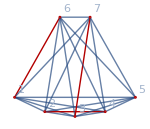
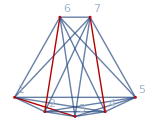
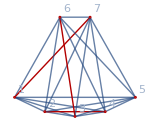
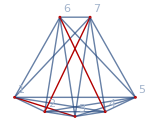
{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}}

```mathematica
Map[Map[GraphFromSymbol[#]&,#[[1]]]&,Take[Select[ShowForNodesTwo[7],Length[Select[#[[1]],HasTrianglePattern[SymbolToSets[#]]&]]==0&],4]]
```

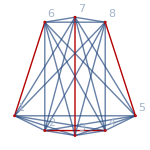
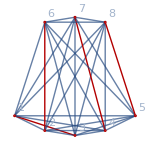
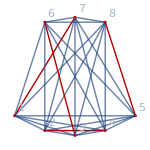
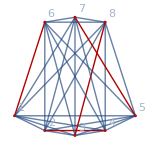
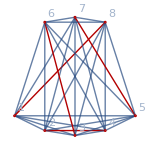
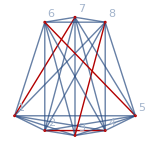
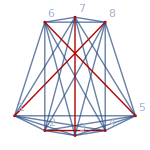
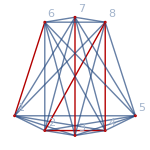
{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-}}

```mathematica
Map[Map[GraphFromSymbol[#]&,#[[1]]]&,Take[Select[ShowForNodesTwo[8],Length[Select[#[[1]],HasTrianglePattern[SymbolToSets[#]]&]]==0&],20]]
```

```mathematica
Clear[ShowForNodes3];ShowForNodes3[nodes_]:=Flatten[Table[
Block[
{
e1=EdgeList[GraphComplement[GraphFromSets[part1]]],
e2=EdgeList[GraphComplement[GraphFromSets[part2]]],
e3=EdgeList[GraphComplement[GraphFromSets[part3]]]
},
{Select[FindFullFormula[ EdgeDelete[CompleteGraph[nodes],DeleteDuplicates[Join[e1,e2,e3]]]], SymbolLevel[#]==4&],{part1,part2,part3}}
]
,

{part1,Take[QuadrilateralsWithPattern[nodes,1],2]},
{part2,Take[QuadrilateralsWithPattern[nodes,2],2]},
{part3,Take[QuadrilateralsWithPattern[nodes,5],2]}
],2]
```

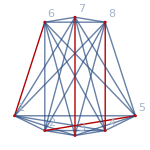
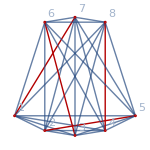
{{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-}}

```mathematica
Map[Map[GraphFromSymbol[#]&,#[[1]]]&,Take[Select[ShowForNodes3[8],Length[Select[#[[1]],HasTrianglePattern[SymbolToSets[#]]&]]==0&],4]]
```